# Draft: code

## May 2018 | merlijn Kersten

The following code was tested for Mathematica 11.2 and Mathematica 11.3.  For questions contact mkersten@amolf.nl or kerstenmerlijn@gmail.com.

To clear all stored variables, run the following block of code:

```mathematica
Remove["Global`*"]
```

The following functions are needed to run the code in this document. The small corrections to the xx-values of tospherical[] are to ensure that the value is not zero, which breaks the function. This small correction does not significantly affect the outcome of any of the calculations presented below.

```mathematica
Needs["ErrorBarPlots`"]
tospherical[{xx_,yy_,zz_}]:={Sqrt[xx^2+yy^2+zz^2],ArcTan[xx,yy],ArcCos[zz/Sqrt[xx^2+yy^2+zz^2]]}
tocartesian[{r_,θ_,ϕ_}] :={r*Cos[θ]*Sin[ϕ],r*Sin[θ]*Sin[ϕ],r*Cos[ϕ]}
```

## Models

The models given below serve to clarify some of the code given below. The first model is an animation of the actual measurement tool: a dodecahedron inside a sphere with a rim. The rim is connected to the dodecahedron with three thin rods. In this plot, and all that follow, coloured lines signify the axis (x: red, y: green, z: blue).

```mathematica
modelrealistic
```

-Graphics3D-

The next model gives the vertices of a dodecahedron (in grey, numbered) and the middle of the faces of a dodecahedron (in red, numbered) which is where the sensors will be.

```mathematica
verticespoints
```

-Graphics3D-

This is a representation of the model used in the code: a unit sphere with a rim ( r = 3 ) around it. The red dots signify the locations of the measurement points of the sensors for twelve points.

```mathematica
modelsphere
```

-Graphics3D-

This model gives the situation for the diffuse lighting: at the origin is a sensor point (red), the rim forms an arch on its sky. The yellow dot is a top/bottom point, the rim does not appear on its sky. The grey dot is the origin of the sphere.

```mathematica
modelshadowdiffuse
```

-Graphics3D-

The next model serves to explain the rationale behind the shading for the direct light. The red vector and ring denote the rim. The green vector denotes a sensor on the sphere, the blue vector the unit vector of the light vector field. The yellow angle is the “shadow vector”: it has unit length, the azimuthal angle of the light (blue) vector and the polar angle of the sensor vector minus the rim vector (in cartesian space, green minus red). If the shadow vector and light vector (nearly) coincide (as they do in this drawing), the sensor is shaded.

```mathematica
modelshadowdirectexplanation
```

-Graphics3D-

The next two models give a top-down (theta) and a side (phi) view of the previous model.

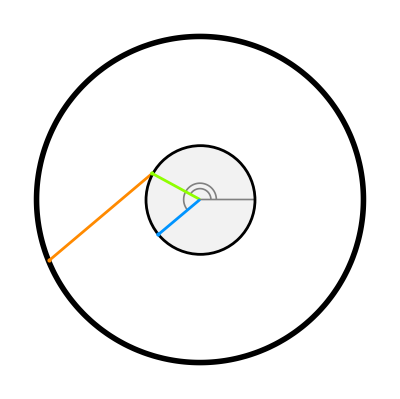

```mathematica
thetaview
```

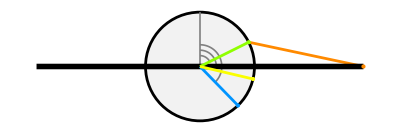

```mathematica
phiview
```

An example of the shading caused by the ring. Once more , the red points are the sensors, the yellow vector is the light field (in reality its norm is at most one), and the black ring is the rim. Black dots on the sphere of the surface denote points that are shaded, either by the rim or by the sphere, and white dots on the sphere of the surface denote points that are illuminated by the vector field. The function can be run again for a different coordinate of the light field (here given in spherical coordinates).

```mathematica
modelshadowdirect[tocartesian[{1,Pi/4,Pi/2-0.2}]]
```

-Graphics3D-

## Code

### Models

```mathematica
modelrealistic =Show[Graphics3D[
{{Opacity[0.07],Sphere[{0,0,0},4]},
{Red,Thickness[0.004],Line[{{0,0,0},{5.5,0,0}}]},
{Green,Thickness[0.004],Line[{{0,0,0},{0,5.5,0}}]},
{Blue,Thickness[0.004],Line[{{0,0,0},{0,0,5.5}}]},
{Black,Thickness[0.0075],Line[{{1.376,0,-0.263},{4,0,0}}]},{Black,Thickness[0.0075],Line[{{-1.114,-0.809,-0.263},{-3.2366,-2.3504,0}}]},
{Black,Thickness[0.0075],Line[{{-1.114,0.809,-0.263},{-3.2366,2.3504,0}}]}
}],PolyhedronData["Dodecahedron"],ParametricPlot3D[
{4*Cos[t],4*Sin[t],0},{t,0,2Pi},PlotStyle->{Black,Thickness[0.02]}
],Boxed->False,ViewPoint->{1,1,.8} ];

datadata = {{0,0,1.114},{0,0,-1.114},{0.308,-0.947,0.498},{-0.308,0.947,-0.498},{0.996,0,0.498},{-0.996,0,-0.498},{0.308,0.947,0.498},{-0.308,-0.947,-0.498},{-0.806,0.585,0.498},{0.806,-0.585,-0.498},{-0.806,-0.585,0.498},{0.806,0.585,-0.498}};
data=PolyhedronData["Dodecahedron","Vertices"];

verticespoints =Show[{Graphics3D[{Gray,PointSize[0.04],Point[data]}],Graphics3D[Text[Position[data,#],1.04 #]&/@data],Graphics3D[{Red,PointSize[0.04],Point[datadata]}],Graphics3D[Text[Position[datadata,#],1.04 #]&/@datadata]},Axes->True,BoxRatios->1];

pointstwelve ={
{0,0,1},
{0,0,-1},
{0.2766,-0.8505,0.4473},
{-0.2766,0.8505,-0.4473},
{0.8944,0,0.4472},
{-0.8944,0,-0.4472},
{0.2766,0.8505,0.4473},
{-0.2766,-0.8505,-0.4473},
{-0.7238,0.5254,0.4472},
{0.7238,-0.5254,-0.4472},
{-0.7238,-0.5254,0.4472},
{0.7238,0.5254,-0.4472}};

modelsphere=Show[Graphics3D[
{{White,Sphere[{0,0,0},1]},
{Opacity[0.06],Sphere[{0,0,0},4]},
{Red,Thickness[0.004],Line[{{0,0,0},{5.5,0,0}}]},
{Green,Thickness[0.004],Line[{{0,0,0},{0,5.5,0}}]},
{Blue,Thickness[0.004],Line[{{0,0,0},{0,0,5.5}}]},
{Red,Point[pointstwelve]}
}],ParametricPlot3D[
{4*Cos[t],4*Sin[t],0},{t,0,2Pi},PlotStyle->{Black,Thickness[0.02]}
],Boxed->False,
ViewPoint->{1,1,.8}  ];
```

### Shade: diffuse lighting

```mathematica
modelshadowdiffuse =Show[{
ParametricPlot3D[
{15Cos[t],15Sin[t],13.415Sin[t]-5},{t,0,2*Pi},PlotStyle->{Black,Thickness[0.02]}],
Graphics3D[{
{Gray,PointSize[Large],Point[{0,0,-5}]},
{PointSize[Large],Red,Point[{0,0,0}]},
{Gray,Line[{{0,0,0},{0,0,-5}}]},
{Opacity[0.09],Sphere[{0,0,-5},5]},
{PointSize[Large],Yellow,Point[{0,-3.6,-1.3}]},
{Gray,Line[{{0,0,-5},{0,-3.6,-1.3}}]}
}]
}];
```

### Shade: direct lighting

```mathematica
rr = tocartesian[{3,0,Pi/2}];
nn = tocartesian[{1,0.8,Pi/2-0.6}];
ll = tocartesian[{1,Pi/2,2.8}];
yellow = tocartesian[{1,tospherical[ll][[2]],tospherical[rr-nn][[3]]}];
gray = tocartesian[{2.95,tospherical[yellow][[2]],Pi/2}]-{-0.6,0,0};
modelshadowdirectexplanation =Show[{Graphics3D[{
{Hue[0.17],Thickness[0.005],Line[{nn,gray}]},
{Hue[0.17],PointSize[Large],Point[gray]},
{Hue[0.24],Thickness[0.005],Line[{{0,0,0},nn}]},
{Hue[0.24],PointSize[Large],Point[nn]},
{Hue[0.57],Thickness[0.005],Line[{{0,0,0},ll}]},
{Hue[0.57],PointSize[Large],Point[ll]},
{Hue[0.09],Thickness[0.005],Line[{{0,0,0},yellow}]},
{Hue[0.09],PointSize[Large],Point[yellow]},
{Opacity[0.15],Ball[{0,0,0},1]}
}],ParametricPlot3D[
{3*Cos[t],3*Sin[t],0},{t,0,2Pi},PlotStyle->{Black,Thickness[0.01]}]},Boxed->False];

shade[light_,point_]:=Module[{},
pointtorim:=tocartesian[{1,tospherical[light][[2]],tospherical[tocartesian[{3,tospherical[light][[2]],Pi/2}]-point][[3]]}];
shadecalculation= If[Dot[Normalize[light],point]>0 && Abs[Dot[Normalize[light],pointtorim]]< 0.997,
0.95,
0];
returns = If[NumericQ[shadecalculation],
shadecalculation,
0]
]

modelshadowdirect[lightcoordinate_]:=Show[{Graphics3D[Table[ {PointSize[Medium],GrayLevel[shade[lightcoordinate,tocartesian[{1,i,j}]]],Point[tocartesian[{1,i,j}]]},{i,Pi/40,79*Pi/40,Pi/40},{j,Pi/40,39*Pi/40,Pi/40}]],
Graphics3D[{
{Gray,Sphere[{0,0,0},1]},
{PointSize[Large],Yellow,Point[4*lightcoordinate]},
{Yellow, Thickness[0.006],Line[{-4*lightcoordinate,4*lightcoordinate}]},
{Red,Thickness[0.004],Line[{{0,0,0},{2,0,0}}]},
{Green,Thickness[0.004],Line[{{0,0,0},{0,2,0}}]},
{Blue,Thickness[0.004],Line[{{0,0,0},{0,0,2}}]},
{Red,PointSize[Medium],Point[pointstwelve]}}],
ParametricPlot3D[
{3*Cos[t],3*Sin[t],0},{t,0,2Pi},PlotStyle->{Black,Thickness[0.02]}]},Boxed->False];

topolar[{xx_,yy_}] :={Sqrt[xx^2+yy^2],ArcTan[yy,xx]};
tocartesian2d[{rr_,θ_}]:={rr*Cos[θ],rr*Sin[θ]}; 
rr = tocartesian2d[{3,Pi/2}];
nn = tocartesian2d[{1,Pi/2-1.107}];
ll = tocartesian2d[{1,2*Pi-0.8}];
orange = tocartesian2d[{1,topolar[{-1,0}+nn][[2]]}];
phiview =Show[{
Graphics[{
{GrayLevel[0.95],Disk[{0,0},1]},
{Black,Thickness[0.005],Circle[{0,0},1]},
{Gray,Thickness[0.003],Line[{{0,0},{0,1}}]},
{Hue[0.09],Thickness[0.005],Line[{nn,{3,0}}]}
}],
ParametricPlot[
{0.2*Cos[t],0.2*Sin[t]},{t,Pi/2-1.107,Pi/2},PlotStyle->{Gray,Thickness[0.003]}],
ParametricPlot[
{0.3*Cos[t],0.3*Sin[t]},{t,Pi/2-topolar[orange][[2]],Pi/2},PlotStyle->{Gray,Thickness[0.003]}],
ParametricPlot[
{0.4*Cos[t],0.4*Sin[t]},{t,2*Pi-0.8,5*Pi/2},PlotStyle->{Gray,Thickness[0.003]}],
Graphics[{
{Black,Thickness[0.01],Line[{{-3,0},{3,0}}]},
{Hue[0.24],Thickness[0.005],Line[{{0,0},nn}]},
{Hue[0.57],Thickness[0.005],Line[{{0,0},ll}]},
{Hue[0.24],PointSize[Large],Point[{nn}]},
{Hue[0.57],PointSize[Large],Point[{ll}]},
{Hue[0.09],PointSize[Large],Point[{3,0}]},
{Hue[0.17],Thickness[0.005],Line[{orange,{0,0}}]},
{Hue[0.17],PointSize[Large],Point[orange]}
}]
},Axes->False];

nntheta = tocartesian2d[{1,Pi-0.5}];
lltheta = tocartesian2d[{1,Pi+0.7}];
orangetheta = {-2.768,-1.121};
thetaview = Show[{
Graphics[{GrayLevel[0.95],Disk[{0,0},1]}],
ParametricPlot[
{3*Cos[t],3*Sin[t]},{t,0,2Pi},PlotStyle->{Black,Thickness[0.01]}],
ParametricPlot[
{0.2*Cos[t],0.2*Sin[t]},{t,Pi-0.5,0},PlotStyle->{Gray,Thickness[0.003]}],
ParametricPlot[
{0.3*Cos[t],0.3*Sin[t]},{t,Pi+0.7,0},PlotStyle->{Gray,Thickness[0.003]}],
Graphics[{
{Hue[0.09],Thickness[0.005],Line[{orangetheta,nntheta}]},
{Gray,Thickness[0.003],Line[{{0,0},{1,0}}]},
{Black,Thickness[0.005],Circle[{0,0},1]},
{Hue[0.24],Thickness[0.005],Line[{{0,0},nntheta}]},
{Hue[0.57],Thickness[0.005],Line[{{0,0},lltheta}]},
{Hue[0.24],PointSize[Large],Point[{nntheta}]},
{Hue[0.57],PointSize[Large],Point[{lltheta}]},
{Hue[0.09],PointSize[Large],Point[orangetheta]}
}]
},Axes->False];
```

## Polyhedrons

The code below gives models of the polyhedrons used in the metric calculation. These can also be found in Appendix A of the writing update.

### Code

```mathematica
Labeled[Show[PolyhedronData["Octahedron"],Boxed->False],"6",Left]
Labeled[Show[PolyhedronData["Cube"],Boxed->False],"8",Left]
Labeled[Show[PolyhedronData["ElongatedSquareDipyramid"],Boxed->False],"10",Left]
Labeled[Show[PolyhedronData["Icosahedron"],Boxed->False],"12",Left]
Labeled[Show[PolyhedronData["CumulatedCube"],Boxed->False],"14",Left]
Labeled[Show[{PolyhedronData[{"Antiprism",7}],Graphics3D[{Black,PointSize[Large],Point[{{0,0,1},{0,0,-1}}]}]},Boxed->False],"16",Left]
Labeled[Show[PolyhedronData["OctahedronThreeCompound"],Boxed->False],"18",Left]
Labeled[Show[PolyhedronData["Dodecahedron"],Boxed->False],"20",Left]
Labeled[Show[PolyhedronData["RhombicIcosahedron"],Boxed->False],"22",Left]
Labeled[Show[PolyhedronData["SmallRhombicuboctahedron"],Boxed->False],"24",Left]
Labeled[Show[PolyhedronData["DisdyakisDodecahedron"],Boxed->False],"26",Left]
```

-Graphics3D-6

-Graphics3D-8

-Graphics3D-10

-Graphics3D-12

-Graphics3D-14

-Graphics3D-16

-Graphics3D-18

-Graphics3D-20

-Graphics3D-22

-Graphics3D-24

-Graphics3D-26

## Choosing number of measurement points

The first problem was to choose the number of measurement points. To this end, the metric was calculated for 11 different number of points (6-26 in steps of 2) for eleven different directness-ratios (0-1 in steps of 0.1).

## Import

Since many functions in the code that follows take minutes or hours to run, the code starts with a few Import-function to import datasets generated by the code. In order for these functions to work, one has to fill in the path of the data files. The data files can be found in the Drive folder, see https://drive.google.com/open?id=1-gFXw8cfpsNAdvKML39-ZWmfgfQuiudS or the folder in the Ehrler group folder. Note that the .mx file only works for Mathematica 11 on Windows.

```mathematica
figureofmeritdata =Flatten[Import["PATH//FigureOfMeritData.csv","Data"]];
comparisondatapart[j_]:=Import[StringJoin["PATH\\comparisondata_",ToString[j],".csv"],"Data"]
```

## Figure of merit

The figure of merit calculates the real value of the metric for a specific value of the diffuseness fraction. It does this by integrating over a sphere of antipodes, see the writing update report.

In the code, this was implemented by defining a function ‘figureofmerit’ that took as arguments the fraction of diffuse light and the coordinates of of the direct light source. It then uses these parameters to define a direct and a diffuse vector field with strength given by the parameter ‘fraction’. Then it defines an illuminance function which adds the direct and diffuse part of the measurement, but again only gives a nonzero value if the dot product between a normal vector of a point on the unit sphere and the light field is nonnegative. This is then used to calculated the actual figure of merit through equation (3) given in the writing update.

```mathematica
figureofmerit[fraction_,coordinates_] := Module[{},
Which[coordinates[[3]] < 0, coordinates[[3]] = Abs[coordinates[[3]]]];

direct :=(1-fraction)*Normalize[coordinates];

diffuse[a_,b_,c_]:=fraction*Normalize[{a,b,c}]; 

illuminance[d_,e_,f_]:=If[
Dot[diffuse[d,e,f],Normalize[{d,e,f}]]≥0,
Dot[diffuse[d,e,f],Normalize[{d,e,f}]],
0
] + If[
Dot[direct,Normalize[{d,e,f}]]≥0,
Dot[direct,Normalize[{d,e,f}]],
0
];

figure = 0.5*NIntegrate[Abs[illuminance[d,e,f]-illuminance[-d,-e,-f]],{d,e,f}∈Ball[{0,0,0},1]]/NIntegrate[illuminance[d,e,f],{d,e,f}∈Ball[{0,0,0},1]]
]
```

The figure of merit is calculated for eleven different values of the fraction between zero and one (in steps of 0.1). The ‘coordinates’ parameter can be chosen arbitrarily: it does not affect the results. The results are saved both as a string (‘figureofmeritdata’) and as an association (‘figureofmeritassociation’) so the can be used for other calculation and/or plotting purposes later. The lines of codes can be run seperately because  ‘figureofmeritdata’ can also be imported (see previous section).

```mathematica
fractionvalues = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1};
```

Note: running the following block of code will take several minutes

```mathematica
figureofmeritdata = Table[figureofmerit[l,{1,1,1}/Sqrt[3]],{l,fractionvalues}];
```

```mathematica
figureofmeritassociation = Association[Table[fractionvalues[[j]]-> Flatten[figureofmeritdata][[j]],{j,1,11}]];
```

### Figure of metric data export

Since it takes several minutes to run the ‘figureofmetricdata’ function, it can be exported after calculation in order to save time if the data is needed in the future.

```mathematica
Export["PATH//FigureOfMeritData.csv",figureofmeritdata];
```

## Metric

The metric calculation requires three variables: the number of measurement points (points), the fraction of diffuse light (fraction), and the coordinates of the light source (coordinates). The metric calculation function starts of by defining the two vector fields used, in the same way as for the figure of merit. 

We wanted to calculate the metric for eleven different number of points between 6 and 26 in steps of 2. In order to do this, we needed the coordinates of these points. We wanted to have an equal spread of antipodes over a unit sphere, in order to get the best results. This problem is similar to the Thomson problem and related Tammes problem, which are related to uniformly distributing electrons and circles, respectively, over a sphere. There are some exact solutions to this problem (for n = 3, 4, 6, 12), some of which were used in this report. When no exact solutions were available, or when they did not suffice (for instance because the points of the solutions were not antipodes), approximate solutions were used by comparing different polyhedrons with the required number of points, based on whether the points were antipodes and whether the points were approximately distributed evenly. The coordinates of these points were obtained by using the vertices of various polyhedrons.

After this, the illuminance was calculated, again in a similar manner as in the figure of merit.%which is similar to the output of the actual sensors. It is a function that calculates the dot product between the normal vector of the points on the sphere (given by normals) and the diffuse and direct fields, respectively. It only calculates this dot product if it is bigger than zero: otherwise it returns zero. This is done because if the dot product is zero, it means that the light is coming from behind the sensor: in the actual situation, this would also yield zero. After this is done, both components are added up. 

Lastly, the metric as defined by equation (2) of the writing update is calculated by first calculating the vector component and then calculating the actual metric. This value is then returned.

```mathematica
metric[points_,fraction_,coordinates_] := Module[{},
Which[coordinates[[3]] < 0, coordinates[[3]] = Abs[coordinates[[3]]]];

direct :=(1-fraction)*Normalize[coordinates];
diffuse[{a_,b_,c_}]:=fraction*Normalize[{a,b,c}];

Which[
points==6,normals=Normalize[#]&/@PolyhedronData["Octahedron","Vertices"], 
points==8,normals=Normalize[#]&/@PolyhedronData["Cube","Vertices"],
points==10,normals=Normalize[#]&/@PolyhedronData["ElongatedSquareDipyramid","Vertices"], 
points==12,normals=Normalize[#]&/@PolyhedronData["Icosahedron","Vertices"],
points==14,normals=Normalize[#]&/@PolyhedronData["CumulatedCube","Vertices"], 
points==16,normals=Append[Append[Normalize[#]&/@PolyhedronData[{"Antiprism",7},"Vertices"],{0,0,1}],{0,0,-1}],
points==18,normals=Normalize[#]&/@PolyhedronData["OctahedronThreeCompound","Vertices"],
points==20,normals=Normalize[#]&/@PolyhedronData["Dodecahedron","Vertices"], 
points==22,normals=Normalize[#]&/@PolyhedronData["RhombicIcosahedron","Vertices"],
points==24,normals=Normalize[#]&/@PolyhedronData["SmallRhombicuboctahedron","Vertices"] ,
points==26,normals=Normalize[#]&/@PolyhedronData["DisdyakisDodecahedron","Vertices"]
];

illuminance[d_]:=If[
Dot[diffuse[d],Normalize[d]]≥0,
Dot[diffuse[d],Normalize[d]],
0
] +If[
Dot[direct,Normalize[d]]≥0,
Dot[direct,Normalize[d]],
0
];

vector[e_] := Abs[illuminance[e]-illuminance[-e]];

 metriccalculation = 0.5*Sum[vector[f],{f,normals}]/Sum[illuminance[g],{g,normals}]
]
```

## Comparison figure of merit and metric

In order to compare the calculated values of the metric, D, to the figure of merit, F.O.M., the relative absolute difference between of them was calculated:

Difference = | D - F.O.M.|/F.O.M.

This yields a number between 0 and infinity, where a zero value means that both measures are equal and a nonzero value gives the percental change in the metric with respect to the figure of merit. As such, it gives an indication of the relative error of the metric. This approach does not work for ratio values of 1.0, since the figure of merit is 0 for these values and thus the difference is infinite.

Note: running the following block of code will take several minutes

```mathematica
comparisondata =Table[
Abs[metric[k,l,RandomPoint[Sphere[]]]-figureofmeritassociation[l]]/figureofmeritassociation[l],
5000,{l,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}},
{k,{6,8,10,12,14,16,18,20,22,24,26}}];
```

### Comparison data export

Since it takes several minutes to run the ‘comparisondata’ function, it can be exported after calculation in order to save time if the data is needed in the future.

```mathematica
comparisondatapart[j_]:=comparisondata[[All,All,j]]
Export[StringJoin["PATH\\comparisondata_",ToString[#],".csv"],comparisondatapart[#]]&/@Range[1,11]
```

## Implementing shadow for n = 12

The following code only calculates the value of the metric for n = 12 while also implementing the effects of shading from the rim around the measurement tool.

## Import

The following code imports the data of the comparison metric for twelve points with shadow, and the figure of merit. Note that the figure of merit data (see previous section) is also needed to run this code.

```mathematica
comparisontwelveshadowdata =Import["PATH//ComparisonTwelveData.csv","Data"];
```

## Metric for twelve points with shadow

This code calculates the metric. It is similar to the metric-code in the previous section, except that it only calculates the metric for n = 12 and that it includes shadows. The diffuse field causes a shadow for the points on the sides of the measurement tool, not for the top or bottom point. This shadow is taken to be a constant. The direct field causes a shadow if there is a vector from the rim to the point that approximately coincides (dot product = 1) with the vector field of the light. In both shading functions, the condition that the light cannot come from behind the sensor is also implemented. 

This version takes as extra argument percentage: this are the diffuse and direct shading values (it represents the thickness of the rim). For the main graph, it’s value is {0.95, 0.997}. In the second graph, this parameter is used to calculate the comparison value for different values of percentage.

The returns = ... function is included in case the previous functions do not return numeric values, which is the case for instance when the tocartesian or tospherical functions break down.

```mathematica
metrictwelvepointswithshadow[fraction_,coordinates_,percentage_] := Module[{},
direct :=(1-fraction)*Normalize[coordinates];

diffuse[{a_,b_,c_}]:=fraction*Normalize[{a,b,c}];

shadediffuse[h_]:=If[Dot[diffuse[h],Normalize[h]]≥0,If[h≠{0,0,1}&&h≠ {0,0,-1},0.974,1],0];

shadedirect[i_,j_]:=Module[{},
pointtorim:=tocartesian[{1,tospherical[i][[2]],tospherical[tocartesian[{3,tospherical[i][[2]],Pi/2}]-j][[3]]}];
shadecalculation= If[Dot[Normalize[i],j]>0 && Abs[Dot[Normalize[i],pointtorim]]< 0.9983,
1,
0];
returns = If[NumericQ[shadecalculation],
shadecalculation,
0]
];

normals = {
{0,0,1},
{0,0,-1},
{0.2766,-0.8505,0.4473},
{-0.2766,0.8505,-0.4473},
{0.8944,0,0.4472},
{-0.8944,0,-0.4472},
{0.2766,0.8505,0.4473},
{-0.2766,-0.8505,-0.4473},
{-0.7238,0.5254,0.4472},
{0.7238,-0.5254,-0.4472},
{-0.7238,-0.5254,0.4472},
{0.7238,0.5254,-0.4472}};

illuminance[d_]:=Dot[diffuse[d],Normalize[d]]*shadediffuse[d] +Dot[direct,Normalize[d]]*shadedirect[Normalize[coordinates],d];

vector[e_] := Abs[illuminance[e]-illuminance[-e]];

metriccalculation = 0.5*Sum[vector[f],{f,normals}]/Sum[illuminance[g],{g,normals}]
]
```

## Comparison metric and figure of metric

The comparison metric is calculated in the same matter as before, only now it is calculated for 10,000 different coordinates, since the metric calculation is significantly easier this time.

```mathematica
comparisontwelveshadowdata =Table[
Table[
Abs[metrictwelvepointswithshadow[l,RandomPoint[Sphere[]],{0.95,0.997}]-figureofmeritassociation[l]]/figureofmeritassociation[l],
10000],{l,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}}];
```

### Export comparison data

```mathematica
Export["PATH//ComparisonTwelveData.csv",comparisontwelveshadowdata];
```